## Set up the metric, compute the Einstein tensor etc.

```mathematica
NotebookDirectory[]
```

/Users/jankozuszek/Documents/Holography with dynamic boundary/

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jankozuszek/Documents/Holography with dynamic boundary

### Metric and reference metric

```mathematica
co = {r,t,x1,x2,x3};
Ndim = Length[co];
```

```mathematica
g=({{0, 1, 0, 0, 0}, {1, -Afun[r,t], 0, 0, 0}, {0, 0, Sfun[r,t]^2, 0, 0}, {0, 0, 0, Sfun[r,t]^2, 0}, {0, 0, 0, 0, Sfun[r,t]^2}});
gup=Inverse[g]//Simplify;
```

### Christoffel Symbols

```mathematica
Chr=Table[
Simplify[(1/2)*Sum[gup[[μ,α]]*(
D[g[[ν,α]],co[[ρ]]]+D[g[[ρ,α]],co[[ν]]]-D[g[[ν,ρ]],co[[α]]]),
{α,1,Ndim}]],
{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim}];
```

### Riemann tensor

```mathematica
Clear[λ]
```

```mathematica
Rdownfun[μ_,ν_,ρ_,σ_]:=Simplify[Sum[g[[μ,λ]](D[Chr[[λ,σ,ν]],co[[ρ]]] - D[Chr[[λ,ρ,ν]],co[[σ]]] + Sum[Chr[[λ,ρ,α]]*Chr[[α,σ,ν]],{α,1,Ndim}]-Sum[Chr[[λ,σ,α]]*Chr[[α,ρ,ν]],{α,1,Ndim}]),{λ,1,Ndim}]];
```

```mathematica
Rdown=Table[Rdownfun[μ,ν,ρ,σ],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim},{σ,1,Ndim}];
```

```mathematica
Riemann=Table[Sum[gup[[μ,λ]]Rdown[[λ,ν,ρ,σ]],{λ,1,Ndim}],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim},{σ,1,Ndim}];
```

### Ricci and Einstein tensors

```mathematica
Ricci=Table[Simplify[Sum[Riemann[[λ,μ,λ,ν]],{λ,1,Ndim}]],{μ,1,Ndim},{ν,1,Ndim}];
R=Sum[gup[[μ,ν]]Ricci[[μ,ν]],{μ,1,Ndim},{ν,1,Ndim}]//Simplify;
Einstein=Ricci-(1/2)R g//Simplify;
```

### Energy-momentum tensor

```mathematica
T=2Simplify[Table[D[Φfun[r,t],co[[μ]]]D[Φfun[r,t],co[[ν]]]-Vfun[Φfun[r,t]]g[[μ,ν]]-1/2 g[[μ]][[ν]]Sum[gup[[α]][[β]]D[Φfun[r,t],co[[α]]]D[Φfun[r,t],co[[β]]],{α,1,Ndim},{β,1,Ndim}],
{μ,1,Ndim},{ν,1,Ndim}]];
divPhi=Simplify[Sum[gup[[μ,ν]]D[D[Φfun[r,t],co[[μ]]],co[[ν]]],{μ,1,Ndim},{ν,1,Ndim}]-Sum[gup[[μ,ν]]Chr[[ρ,μ,ν]]D[Φfun[r,t],co[[ρ]]],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim}]]
```

Afun^(1,0)[r,t] Φfun^(1,0)[r,t]+(3 (Φfun^(0,1)[r,t] Sfun^(1,0)[r,t]+(Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]) Φfun^(1,0)[r,t]))/Sfun[r,t]+2 Φfun^(1,1)[r,t]+Afun[r,t] Φfun^(2,0)[r,t]

## Equations of motion

```mathematica
Clear[Afun,Sfun,Φfun,Vfun]
```

```mathematica
Eqs=Simplify[gup.(Einstein-T)];
```

```mathematica
eq1=Simplify[Eqs[[2,1]]]
```

-2 (Φfun^(1,0)[r,t])^2-(3 Sfun^(2,0)[r,t])/Sfun[r,t]

```mathematica
soleq1=Solve[0==eq1,Derivative[2,0][Sfun][r,t]][[1]]
```

{Sfun^(2,0)[r,t]→-2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2}

```mathematica
eq2=Simplify[Eqs[[2,2]]//.soleq1]
```

2 Vfun[Φfun[r,t]]+(3 Sfun^(1,0)[r,t] (2 Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]))/Sfun[r,t]^2-Afun[r,t] (Φfun^(1,0)[r,t])^2+(3 (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]+2 Sfun^(1,1)[r,t]))/(2 Sfun[r,t])

```mathematica
eq3=divPhi-Vfun'[Φfun[r,t]];
```

```mathematica
eq4=Eqs[[3,3]]//Simplify
```

2 Vfun[Φfun[r,t]]+(Sfun^(1,0)[r,t] (2 Sfun^(0,1)[r,t]+Afun[r,t] Sfun^(1,0)[r,t]))/Sfun[r,t]^2+2 Φfun^(0,1)[r,t] Φfun^(1,0)[r,t]+Afun[r,t] (Φfun^(1,0)[r,t])^2+1/2 Afun^(2,0)[r,t]+(2 (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]+2 Sfun^(1,1)[r,t]+Afun[r,t] Sfun^(2,0)[r,t]))/Sfun[r,t]

```mathematica
eq5=2 Sfun[r,t]Eqs[[1,2]]//Simplify
```

-4 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])-3 (2 Sfun^(0,2)[r,t]-Sfun^(0,1)[r,t] Afun^(1,0)[r,t]+Afun^(0,1)[r,t] Sfun^(1,0)[r,t]+2 Afun[r,t] Sfun^(1,1)[r,t])

```mathematica
sys={eq1,eq2,eq3,eq4,eq5};
```

## Expansion near the boundary: Eddington-Finkelstein

```mathematica
ASPfilename="ASPsol.txt";
```

```mathematica
Clear[Afun,Sfun,Φfun,Vfun];
```

```mathematica
sysScaled={r^2 sys[[1]],sys[[2]],r sys[[3]],sys[[4]],1/r^2 sys[[5]]}//Simplify;
```

```mathematica
order=6;
```

```mathematica
Vfun[x_]:=1/2 (-x+x^3/4)^2-4/3 (-3/2-x^2/2+x^4/16)^2;
```

```mathematica
Simplify[Vfun'[x]]
```

-1/48 x (144+64 x^2-33 x^4+2 x^6)

```mathematica
ASer[r_,t_,ord_]:=(r)^2 Sum[(Subscript[a, n][t]+Subscript[α1, n][t]Log[r]+Subscript[α2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
SSer[r_,t_,ord_]:=(r)Sum[(Subscript[s, n][t]+Subscript[σ1, n][t]Log[r]+Subscript[σ2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
PhiSer[r_,t_,ord_]:=(1/r)Sum[(Subscript[p, n][t]+Subscript[ψ1, n][t]Log[r]+Subscript[ψ2, n][t] Log[r]^2)(1/r)^n,{n,0,ord}];
```

```mathematica
BCs={Subscript[a, 0][t]->1,Subscript[a, 1][t]->2 ξ[t],Subscript[s, 0][t]->S0[t],Subscript[p, 0][t]->M};
```

```mathematica
LogToDel={Log[r]->δ};
```

```mathematica
sola4={Subscript[a, 4]'[t]->2/27 (36 M^2 ξ[t] ξ'[t]-18 M Subscript[p, 2]'[t]+(36 M^2 ξ[t]^2 S0'[t])/S0[t]+(9 M^2 S0'[t] S0''[t])/S0[t]^2+(2 ((4 M^4-27 Subscript[a, 4][t]-18 M Subscript[p, 2][t]) S0'[t]+6 M^2 Derivative[3][S0][t]))/S0[t])};
```

```mathematica
sol=BCs;
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Afun[r_,t_]=ASer[r,t,ii]//.sol;
Sfun[r_,t_]=SSer[r,t,ii]//.sol;
Φfun[r_,t_]=PhiSer[r,t,ii]//.sol;

sysCoeff=SeriesCoefficient[sysScaled,{r,Infinity,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];

EqHere=Join[EqHereL0,EqHereL1,EqHereL2];

VarsHere={Subscript[a, ii][t],Subscript[p, ii][t],Subscript[s, ii][t],Subscript[α1, ii][t],Subscript[α2, ii][t],Subscript[σ1, ii][t],Subscript[σ2, ii][t],Subscript[ψ1, ii][t],Subscript[ψ2, ii][t]};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[sysScaled,{r,Infinity,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,0,order}]
][[1]]]
```

Order = 0, time = 0.673994, equation check = {0,0,0,0,0}

Order = 1, time = 0.660167, equation check = {0,0,0,0,0}

Order = 2, time = 0.808379, equation check = {0,0,0,0,0}

Order = 3, time = 1.39843, equation check = {0,0,0,0,0}

Order = 4, time = 2.27337, equation check = {0,0,0,0,0}

Order = 5, time = 6.01686, equation check = {0,0,0,0,0}

Order = 6, time = 19.3582, equation check = {0,0,0,0,0}

Total time: 31.1898

```mathematica
ASPsol=sol;
```

```mathematica
Put[ASPsol,ASPfilename];
```

## Expansion near the boundary: Fefferman-Graham

```mathematica
(*order=5;*)
```

In these coords, w =√ρ, the usual FG coordinate and z=r_EF^-1.

```mathematica
(*Clear[REF,TEF,G11,G22,A,CoEq,τ,r,ZEF,Afun]*)
```

```mathematica
(*FGco={w,t};
EFco={ZEF[w,t],TEF[w,t]};*)
```

```mathematica
(*ΛMat=Table[D[EFco[[μ]],FGco[[ν]]],{μ,1,2},{ν,1,2}];*)
```

```mathematica
(*FGmetric=DiagonalMatrix[{1/w^2,G11[w,t]}];*)
```

```mathematica
(*EFmetric={{0,-1/ZEF[w,t]^2},{-1/ZEF[w,t]^2,-Afun[1/ZEF[w,t],TEF[w,t]]}};*)
```

```mathematica
(*CoEq=Simplify[FGmetric-Transpose[ΛMat].EFmetric.ΛMat];*)
```

```mathematica
(*CoEq//MatrixForm*)
```

(1/w^2+Afun[1/ZEF[w,t],TEF[w,t]] (TEF^(1,0)[w,t])^2+(2 TEF^(1,0)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2 | (Afun[1/ZEF[w,t],TEF[w,t]] ZEF[w,t]^2 TEF^(0,1)[w,t] TEF^(1,0)[w,t]+ZEF^(0,1)[w,t] TEF^(1,0)[w,t]+TEF^(0,1)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2
(Afun[1/ZEF[w,t],TEF[w,t]] ZEF[w,t]^2 TEF^(0,1)[w,t] TEF^(1,0)[w,t]+ZEF^(0,1)[w,t] TEF^(1,0)[w,t]+TEF^(0,1)[w,t] ZEF^(1,0)[w,t])/ZEF[w,t]^2 | G11[w,t]+TEF^(0,1)[w,t] (Afun[1/ZEF[w,t],TEF[w,t]] TEF^(0,1)[w,t]+(2 ZEF^(0,1)[w,t])/ZEF[w,t]^2))

```mathematica
(*ZEFSer[w_,t_,ord_]:=Sum[(Subscript[Ρ, n][t]+Subscript[ρ1, n][t]Log[w](*+Subscript[ρ2, n][t] Log[w]^2*))w^n,{n,1,ord}];
TEFSer[w_,t_,ord_]:=t+Sum[(Subscript[Τ, n][t]+Subscript[τ1, n][t]Log[w](*+Subscript[τ2, n][t] Log[w]^2*))w^n,{n,1,ord}];*)
```

```mathematica
(*G11[w_,t_]:=-1/w^2+Sum[(Subscript[G0, n][t]+Subscript[G1, n][t]Log[w]+Subscript[G2, n][t] Log[w]^2)w^n,{n,0,order}];*)
```

```mathematica
(*CoordEq=w^3{CoEq[[1,1]],CoEq[[1,2]]};*)
```

```mathematica
(*sol={Subscript[τ1, 1][t]->0,Subscript[Τ, 1][t]->-1};
LogToDel={Log[w]->δ};
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Afun[r_,t_]=ASer[r,t,ii]//.ASPsol;
ZEF[w_,t_]=ZEFSer[w,t,ii]//.sol;
TEF[w_,t_]=TEFSer[w,t,ii]//.sol;

sysCoeff=SeriesCoefficient[CoordEq,{w,0,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
(*EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];*)

EqHere=Join[EqHereL0,EqHereL1(*,EqHereL2*)];

VarsHere={Subscript[Ρ, ii][t],Subscript[Τ, ii][t],Subscript[ρ1, ii][t](*,Subscript[ρ2, ii][t]*),Subscript[τ1, ii][t](*,Subscript[τ2, ii][t]*)};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[CoordEq,{w,0,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,1,order}]
][[1]]]*)
```

Order = 1, time = 0.055222, equation check = {0,0}

Order = 2, time = 1.33436, equation check = {0,0}

Order = 3, time = 0.466835, equation check = {0,0}

Order = 4, time = 13.7499, equation check = {0,0}

Order = 5, time = 99.6919, equation check = {0,0}

Total time: 115.299

```mathematica
(*FGsol=sol;*)
```

```mathematica
(*GttExpr=-w^2(TEF^(0,1)[w,t] (Afun[1/ZEF[w,t],TEF[w,t]] TEF^(0,1)[w,t]+(2 ZEF^(0,1)[w,t])/ZEF[w,t]^2))//.FGsol;*)
```

```mathematica
(*Gtt0=SeriesCoefficient[GttExpr,{w,0,0}]//Simplify*)
```

-1

```mathematica
(*Gtt2=SeriesCoefficient[GttExpr,{w,0,2}]//Simplify*)
```

M^2/3-S_0'[t]^2/(2 S_0[t]^2)+S_0''[t]/S_0[t]

```mathematica
(*Gtt4=SeriesCoefficient[GttExpr,{w,0,4}]//.{Log[1/w]->0}//Simplify*)
```

$Aborted

```mathematica
(*Htt4=-1/2 Coefficient[SeriesCoefficient[GttExpr,{w,0,4}],Log[1/w]]//Simplify*)
```

(M^2 S_0''[t])/(4 S_0[t])

```mathematica
(*GxxExpr=w^2 SSer[1/ZEF[w,t],TEF[w,t],order]^2;*)
```

```mathematica
(*Gxx0=SeriesCoefficient[GxxExpr,{w,0,0}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify*)
```

S_0[t]^2

```mathematica
(*Gxx2=SeriesCoefficient[GxxExpr,{w,0,2}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}]]//Simplify*)
```

1/6 (-2 M^2 S_0[t]^2-3 S_0'[t]^2)

```mathematica
(*Gxx4=SeriesCoefficient[GxxExpr,{w,0,4}]//.Join[{Log[1/w]->0},FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]]//Simplify*)
```

(4 (19 M^4+72 M^2 ξ[t]^2-27 a_4[t]-72 M p_2[t]) S_0[t]^4+27 S_0'[t]^4+204 M^2 S_0[t]^3 S_0''[t])/(432 S_0[t]^2)

```mathematica
(*Hxx4=-1/2Coefficient[SeriesCoefficient[GxxExpr,{w,0,4}]//.Join[FGsol,ASPsol,D[ASPsol,t],D[ASPsol,{t,2}],D[ASPsol,{t,2}],D[ASPsol,{t,3}],D[ASPsol,{t,4}]],Log[1/w]]//Simplify*)
```

-1/12 M^2 (2 S_0'[t]^2+S_0[t] S_0''[t])

## Evolution equations

```mathematica
Clear[Afun,Sfun,Φfun,Vfun]
```

```mathematica
D[f[r,t],{t,2}]
```

f^(0,2)[r,t]

```mathematica
replDDt={Derivative[0,2][f_][r,t]->Subscript[f, dd][r,t]-(1/2 Derivative[0,1][Afun][r,t]Derivative[1,0][f][r,t]+Afun[r,t]Derivative[1,1][f][r,t]+1/4 Afun[r,t]Derivative[1,0][Afun][r,t]Derivative[1,0][f][r,t]+1/4 Afun[r,t]^2 Derivative[2,0][f][r,t]) };
```

```mathematica
replDt={Derivative[0,1][f_][r,t]->Subscript[f, d][r,t]-1/2 Afun[r,t]Derivative[1,0][f][r,t]};
```

```mathematica
replDrDt=D[replDt,r]//Simplify;
```

```mathematica
sol1=Solve[0==eq1,Derivative[2,0][Sfun][r,t]][[1]]//Simplify
```

{Sfun^(2,0)[r,t]→-2/3 Sfun[r,t] (Φfun^(1,0)[r,t])^2}

```mathematica
tmp=sys[[2]]//.replDrDt//.replDt//.sol1//Simplify;
```

```mathematica
sol2=Solve[0==tmp,Derivative[1,0][Subscript[Sfun, d]][r,t]][[1]]//Simplify
```

{Sfun_d^(1,0)[r,t]→-2/3 Sfun[r,t] Vfun[Φfun[r,t]]-(2 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]}

```mathematica
tmp=sys[[3]]//.replDrDt//.replDt//Simplify;
```

```mathematica
sol3=Solve[0==tmp,Derivative[1,0][Subscript[Φfun, d]][r,t]][[1]]//Simplify//Expand
```

{Φfun_d^(1,0)[r,t]→1/2 Vfun'[Φfun[r,t]]-(3 Φfun_d[r,t] Sfun^(1,0)[r,t])/(2 Sfun[r,t])-(3 Sfun_d[r,t] Φfun^(1,0)[r,t])/(2 Sfun[r,t])}

```mathematica
tmp=sys[[4]]//.replDrDt//.replDt//.sol1//.sol2//Simplify;
```

```mathematica
sol4=Solve[0==tmp,Derivative[2,0][Afun][r,t]][[1]]//Simplify//Expand
```

{Afun^(2,0)[r,t]→4/3 Vfun[Φfun[r,t]]+(12 Sfun_d[r,t] Sfun^(1,0)[r,t])/Sfun[r,t]^2-4 Φfun_d[r,t] Φfun^(1,0)[r,t]}

```mathematica
tmp=sys[[5]]//.replDDt//.replDrDt//.replDt//.Join[sol1,sol2,sol3,sol4]//Simplify;
```

```mathematica
tmp
```

-6 Sfun_dd[r,t]-4 Sfun[r,t] Φfun_d[r,t]^2+3 Sfun_d[r,t] Afun^(1,0)[r,t]

```mathematica
sol5=Solve[0==tmp,Subscript[Sfun, dd][r,t]][[1]]//Simplify//Expand
```

{Sfun_dd[r,t]→-2/3 Sfun[r,t] Φfun_d[r,t]^2+1/2 Sfun_d[r,t] Afun^(1,0)[r,t]}

```mathematica
evolEqs={Derivative[2,0][Sfun][r,t]-(Derivative[2,0][Sfun][r,t]/.sol1),Derivative[1,0][Subscript[Sfun, d]][r,t]-(Derivative[1,0][Subscript[Sfun, d]][r,t]/.sol2),Derivative[1,0][Subscript[Φfun, d]][r,t]-(Derivative[1,0][Subscript[Φfun, d]][r,t]/.sol3),Derivative[2,0][Afun][r,t]-(Derivative[2,0][Afun][r,t]/.sol4)};
```

```mathematica
constrEq=Subscript[Sfun, dd][r,t]-(Subscript[Sfun, dd][r,t]/.sol5);
```

## ‘Subtracted’ variables

```mathematica
order=5;
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,ii,S0];
```

```mathematica
SdotSer[r_,t_,ord_]:=(r)^2 Sum[(Subscript[sd, n][t]+Subscript[σd1, n][t]Log[r](*+Subscript[σd2, n][t] Log[r]^2*))(1/r)^n,{n,0,ord}];
```

```mathematica
PhidotSer[r_,t_,ord_]:=Sum[(Subscript[pd, n][t]+Subscript[ψd1, n][t]Log[r](*+Subscript[ψd2, n][t] Log[r]^2*))(1/r)^n,{n,0,ord}];
```

```mathematica
dotdef={1/r^2(Sdot[r,t]-(D[Sfun[r,t],t]+1/2 Afun[r,t]D[Sfun[r,t],r])),Phidot[r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r])};
```

```mathematica
sol={Subscript[ψd1, 0][t]->0};
LogToDel={Log[r]->δ};
Print["Total time: ",AbsoluteTiming[
Do[
Print["Order = ",ii,", time = ",AbsoluteTiming[
Sdot[r_,t_]=SdotSer[r,t,ii]//.sol;
Phidot[r_,t_]=PhidotSer[r,t,ii]//.sol;

Afun[r_,t_]=ASer[r,t,ii]//.ASPsol;
Sfun[r_,t_]=SSer[r,t,ii]//.ASPsol;
Φfun[r_,t_]=PhiSer[r,t,ii]//.ASPsol;

sysCoeff=SeriesCoefficient[dotdef,{r,Infinity,ii}]//.LogToDel//Simplify;
EqHereL0=SeriesCoefficient[sysCoeff,{δ,0,0}];
EqHereL1=SeriesCoefficient[sysCoeff,{δ,0,1}];
(*EqHereL2=SeriesCoefficient[sysCoeff,{δ,0,2}];*)

EqHere=Join[EqHereL0,EqHereL1(*,EqHereL2*)];

VarsHere={Subscript[sd, ii][t],Subscript[pd, ii][t],Subscript[σd1, ii][t],(*Subscript[σd2, ii][t],*)Subscript[ψd1, ii][t](*,Subscript[ψd2, ii][t]*)};
DtVarsHere=D[VarsHere,t];

solHere=Solve[0==EqHere,Join[VarsHere,DtVarsHere]][[1]]//Quiet;
solHere2=DeleteCases[solHere,Derivative[_][_][_]->_];
sol=Join[sol,solHere2];

check=SeriesCoefficient[dotdef,{r,Infinity,ii}]//.sol//.D[sol,t]//.sola4//Simplify;
][[1]],", equation check = ",check];
,{ii,0,order}]
][[1]]]
```

Order = 0, time = 0.009232, equation check = {0,0}

Order = 1, time = 0.015061, equation check = {0,0}

Order = 2, time = 0.087694, equation check = {0,0}

Order = 3, time = 0.157197, equation check = {0,0}

Order = 4, time = 0.363274, equation check = {0,0}

Order = 5, time = 0.773254, equation check = {0,0}

Total time: 1.40602

```mathematica
PSDotSol=sol;
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,ii];
```

```mathematica
replWithSub={
Afun[r,t]->((r^2 Subscript[a, 0][t]+r Subscript[a, 1][t]+Subscript[a, 2][t]+(Log[r] Subscript[α1, 4][t])/r^2+(Log[r] Subscript[α1, 5][t])/r^3)/.ASPsol)+ASub[r,t]/r^2,
Sfun[r,t]->(((r Subscript[s, 0][t]+Subscript[s, 1][t]+(Subscript[s, 2][t])/r+(Subscript[s, 3][t])/r^2)+((Log[r] Subscript[σ1, 4][t])/r^3+(Log[r] Subscript[σ1, 5][t])/r^4+(Log[r] Subscript[σ1, 6][t])/r^5)+(Log[r]^2 Subscript[σ2, 6][t])/r^5)//.ASPsol)+SSub[r,t]/r^3,
Φfun[r,t]->((((Subscript[p, 0][t])/r+(Subscript[p, 1][t])/r^2)+((Log[r] Subscript[ψ1, 2][t])/r^3+(Log[r] Subscript[ψ1, 3][t])/r^4))/.ASPsol)+PhiSub[r,t]/r^3,
Subscript[Sfun, d][r,t]->(((r^2 Subscript[sd, 0][t]+r Subscript[sd, 1][t]+Subscript[sd, 2][t]+(Subscript[sd, 3][t])/r)+((Log[r] Subscript[σd1, 4][t])/r^2+(Log[r] Subscript[σd1, 5][t])/r^3))/.PSDotSol)+SdotSub[r,t]/r^2,
Subscript[Φfun, d][r,t]->((Subscript[pd, 0][t]+((Log[r] Subscript[ψd1, 2][t])/r^2+(Log[r] Subscript[ψd1, 3][t])/r^3))/.PSDotSol)+PhidotSub[r,t]/r^2

};
```

```mathematica
Clear[S0]
```

```mathematica
Clear[Sdot,Sfun,Phidot,Φfun,Afun,ii];
```

```mathematica
replWithSub=Join[replWithSub,D[replWithSub,r],D[replWithSub,{r,2}]]//Simplify;
```

```mathematica
ScaledEvolEqs={r^3 evolEqs[[1]],r^2 evolEqs[[2]],r^2 evolEqs[[3]],evolEqs[[4]]}//.replWithSub;
```

```mathematica
SeriesCoefficient[PhiSer[r,t,2],{r,Infinity,3}]//.ASPsol//Expand//Simplify
```

p_2[t]-(M Log[r] (S0'[t]^2+S0[t] S0''[t]))/(2 S0[t]^2)

#### Boundary conditions

```mathematica
tmp=r^2(SdotSer[r,t,4]-(((r^2 Subscript[sd, 0][t]+r Subscript[sd, 1][t]+Subscript[sd, 2][t]+(Subscript[sd, 3][t])/r)+((Log[r] Subscript[σd1, 4][t])/r^2+(Log[r] Subscript[σd1, 5][t])/r^3))))//.PSDotSol//Simplify;
```

```mathematica
SeriesCoefficient[tmp,{r,Infinity,0}]//Simplify//Expand
```

-5/36 M^4 S0[t]-1/2 M^2 S0[t] ξ[t]^2+1/2 S0[t] a_4[t]+1/2 M S0[t] p_2[t]+2/9 M^2 ξ[t] S0'[t]+(3 M^2 S0'[t]^2)/(16 S0[t])-61/144 M^2 S0''[t]

```mathematica
tmp=r^2(ASer[r,t,4]-((r^2 Subscript[a, 0][t]+r Subscript[a, 1][t]+Subscript[a, 2][t]+(Log[r] Subscript[α1, 4][t])/r^2+(Log[r] Subscript[α1, 5][t])/r^3)))//.ASPsol//Simplify;
```

```mathematica
Series[tmp,{r,Infinity,0}]
```

a_4[t]+O[1/r]^1

## Final equations

### Compute

```mathematica
Clear[SSub,PhiSub,S0,ξ,M,Vfun,SdotSub]
```

```mathematica
RtoZ={Derivative[2,0][f_][r,t]->z^4 Derivative[2,0][f][z,t]+2 z^3 Derivative[1,0][f][z,t],Derivative[1,0][f_][r,t]->-z^2 Derivative[1,0][f][z,t],f_[r,t]->f[z,t],r->1/z};
```

```mathematica
expr=(((r^2 Subscript[sd, 0][t]+r Subscript[sd, 1][t]+Subscript[sd, 2][t]+(Subscript[sd, 3][t])/r)+((Log[r] Subscript[σd1, 4][t])/r^2+(Log[r] Subscript[σd1, 5][t])/r^3)))+SdotSub[r,t]/r^2
```

SdotSub[r,t]/r^2+r^2 sd_0[t]+r sd_1[t]+sd_2[t]+sd_3[t]/r+(Log[r] σd1_4[t])/r^2+(Log[r] σd1_5[t])/r^3

```mathematica
expr//.RtoZ
```

z^2 SdotSub[z,t]+sd_0[t]/z^2+sd_1[t]/z+sd_2[t]+z sd_3[t]+z^2 Log[1/z] σd1_4[t]+z^3 Log[1/z] σd1_5[t]

```mathematica
Subscript[σd1, 5][t]//.PSDotSol//Simplify
```

(M^2 (5 S0'[t]^3+3 S0[t] S0'[t] (5 ξ[t] S0'[t]-3 S0''[t])+S0[t]^2 (-5 ξ[t] S0''[t]+2 S0^(3)[t])))/(30 S0[t]^2)

```mathematica
replDS0=Table[D[S0[t],{t,ii}]->ToExpression["DS"<>ToString[ii]][t],{ii,0,6}];
```

```mathematica
toODE={Derivative[2,0][f_][z,t]->f''[z],Derivative[1,0][f_][z,t]->f'[z],f_[z,t]->f[z]};
```

```mathematica
tmpeq=ScaledEvolEqs[[1]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
SEq=z^-4 tmpeq//.toODE//Simplify;
```

```mathematica
tmpeq=ScaledEvolEqs[[2]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
SdotEq=-z^-2 tmpeq//.toODE//Simplify;
```

```mathematica
tmpeq=ScaledEvolEqs[[3]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
PhidotEq=-z^-2 tmpeq//.toODE//Simplify;
```

```mathematica
tmpeq=ScaledEvolEqs[[4]]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
AEq=z^-6 tmpeq//.toODE//Simplify;
```

```mathematica
finaleqs={SEq,SdotEq,PhidotEq,AEq};
```

```mathematica
{Coefficient[SEq,SSub''[z]],Coefficient[SdotEq,SdotSub'[z]],Coefficient[PhidotEq,PhidotSub'[z]],Coefficient[AEq,ASub''[z]]}//Simplify
```

{1,1,1,1}

```mathematica
SCoeffs=Reverse[{Coefficient[SEq,SSub''[z]],Coefficient[SEq,SSub'[z]],Coefficient[SEq,SSub[z]],SEq//.{SSub[z]->0,SSub'[z]->0,SSub''[z]->0}}]//Simplify;
```

```mathematica
Simplify[SEq-SCoeffs.{1,SSub[z],SSub'[z],SSub''[z]}]
```

0

```mathematica
SdotCoeffs=Reverse[{Coefficient[SdotEq,SdotSub'[z]],Coefficient[SdotEq,SdotSub[z]],SdotEq//.{SdotSub[z]->0,SdotSub'[z]->0}}]//Simplify;
```

```mathematica
Simplify[SdotEq-SdotCoeffs.{1,SdotSub[z],SdotSub'[z]}]
```

0

```mathematica
PhidotCoeffs=Reverse[{Coefficient[PhidotEq,PhidotSub'[z]],Coefficient[PhidotEq,PhidotSub[z]],PhidotEq//.{PhidotSub[z]->0,PhidotSub'[z]->0}}]//Simplify;
```

```mathematica
Simplify[PhidotEq-PhidotCoeffs.{1,PhidotSub[z],PhidotSub'[z]}]
```

0

```mathematica
ACoeffs=Reverse[{Coefficient[AEq,ASub''[z]],Coefficient[AEq,ASub'[z]],Coefficient[AEq,ASub[z]],AEq//.{ASub[z]->0,ASub'[z]->0,ASub''[z]->0}}]//Simplify;
```

```mathematica
Simplify[AEq-ACoeffs.{1,ASub[z],ASub'[z],ASub''[z]}]
```

0

```mathematica
cosmocoeffs={SCoeffs,SdotCoeffs,PhidotCoeffs,ACoeffs};
```

```mathematica
Vars={PhiSub[z],SSub[z],SdotSub[z],PhidotSub[z],ASub[z]};
varnames={"Phi","S","Sdot","Phidot","A"};
```

```mathematica
replfun=Table[{Vars[[ii]]->ToExpression[varnames[[ii]]],D[Vars[[ii]],z]->ToExpression[varnames[[ii]]<>"Z"],D[Vars[[ii]],{z,2}]->ToExpression[varnames[[ii]]<>"ZZ"]},{ii,1,Length[Vars]}]//Flatten;
replfun=Join[replfun,{ξ[t]->X,Vfun'[x_]->DV[x],Subscript[p, 2][t]->p2,Subscript[a, 4][t]->a4,Log[1/z]->LN}];
```

```mathematica
Clear[S0]
```

```mathematica
Sform[t_]:=Exp[(H t)/2](Cosh[Om (t-tstar)]/Cosh[Om*tstar])^(H/(2Om));
```

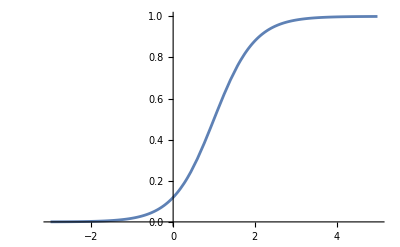

```mathematica
Plot[Sform'[t]/Sform[t]//.{H->1,Om->1,tstar->1},{t,-3,5}]
```

```mathematica
Sform[t]//.{H->1,Om->1,tstar->1}//Simplify
```

ⅇ^(t/2) √Cosh[1-t] √Sech[1]

```mathematica
Sech[1]//N
```

0.648054

```mathematica
Limit[Sform[x],x->-Infinity]
```

ⅇ^(1/2 (1-Log[2]))

```mathematica
Sform[t_]:=ⅇ^(t/2) √Cosh[1-t]/N[ⅇ^(1/2 (1-Log[2])),10];
```

```mathematica
Plot[Sform'[t]/Sform[t],{t,-3,5}]
```

-Graphics-

```mathematica
Sform[t]//CForm
```

0.857763885*Power(E,t/2.)*Sqrt(Cosh(1 - t))

```mathematica
replDS0
```

{S0[t]→DS0[t],S0'[t]→DS1[t],S0''[t]→DS2[t],S0^(3)[t]→DS3[t],S0^(4)[t]→DS4[t],S0^(5)[t]→DS5[t],S0^(6)[t]→DS6[t]}

```mathematica
D[Sform[t],{t,0}]
```

0.857763885 ⅇ^(t/2) √Cosh[1-t]

### Write out coefficients

```mathematica
ODEdegree={2,1,1,2};
```

```mathematica
dependence="(Phi,PhiZ,PhiZZ, S,SZ,SZZ, Sdot,SdotZ,SdotZZ, Phidot,PhidotZ,PhidotZZ, A,AZ,AZZ, z,LN, t, X, p2, a4)";
```

```mathematica
str="";
For[ii = 0, ii<=6,ii++,
str=str<>"function DS"<>ToString[ii]<>"(t)\n\n";
str=str<>"res = "<>ToString[Simplify[D[Sform[t],{t,ii}]]//CForm]<>"; \n\n";
str=str<>"return res;\nend\n\n";
];

For[var=1,var<=4,var++,
For[ii=0,ii<2,ii++,
str=str<>"function "<>varnames[[var+1]]<>"Coeff"<>ToString[ii]<>dependence<>"\n\n";
str=str<>"co = "<>ToString[cosmocoeffs[[var,ii+2]]//.replfun//.replDS0//CForm]<>"; \n\n";
str=str<>"return co;\nend\n\n";
];
str=str<>"function "<>varnames[[var+1]]<>"Src"<>dependence<>"\n\n";
str=str<>"co = "<>ToString[cosmocoeffs[[var,1]]//.replfun//.replDS0//CForm]<>"; \n\n";
str=str<>"return co;\nend\n\n";
];
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
(*strfile=OpenWrite["Julia practice/CosmoCoeffExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

### Flat expressions

```mathematica
S0[t_]:=1;
```

```mathematica
flatSCoeffs=Simplify[SCoeffs];
flatSdotCoeffs=Simplify[SdotCoeffs];
flatPhidotCoeffs=Simplify[PhidotCoeffs];
flatACoeffs=Simplify[ACoeffs];
```

```mathematica
flatcoeffs={flatSCoeffs,flatSdotCoeffs,flatPhidotCoeffs,flatACoeffs};
```

```mathematica
flateqs=Simplify[{finaleqs[[1]],finaleqs[[2]],finaleqs[[3]],finaleqs[[4]]}]//Expand;
```

```mathematica
flatSCoeffs
```

{(2 (3 M^2 (-1+3 z ξ[t])+(3-M^2 z^2+z (3+M^2 z^2) ξ[t]) (M+3 z^2 PhiSub[z]-2 M z ξ[t]+z^3 PhiSub'[z])^2))/(9 z^4),(72+4 z^2 (M+3 z^2 PhiSub[z]-2 M z ξ[t]+z^3 PhiSub'[z])^2)/(6 z^2),8/z,1}

### Write out flat coefficients

```mathematica
(*ODEdegree={2,1,1,2};*)
```

```mathematica
(*dependence="(Phi,PhiZ,PhiZZ, S,SZ,SZZ, Sdot,SdotZ,SdotZZ, Phidot,PhidotZ,PhidotZZ, A,AZ,AZZ, z,LN, t, X, p2, a4)";*)
```

```mathematica
(*str="";
For[var=1,var<=4,var++,
For[ii=0,ii<2,ii++,
str=str<>"function "<>varnames[[var+1]]<>"Coeff"<>ToString[ii]<>dependence<>"\n\n";
str=str<>"co = "<>ToString[flatcoeffs[[var,ii+2]]//.replfun//CForm]<>"; \n\n";
str=str<>"return co;\nend\n\n";
];
str=str<>"function "<>varnames[[var+1]]<>"Src"<>dependence<>"\n\n";
str=str<>"co = "<>ToString[flatcoeffs[[var,1]]//.replfun//CForm]<>"; \n\n";
str=str<>"return co;\nend\n\n";
];*)
```

```mathematica
(*str=StringReplace[str,".*" ->"."<>" "<>"*"];*)
```

```mathematica
(*strfile=OpenWrite["Julia practice/FlatCoeffExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

### Write out whole equations

```mathematica
(*str="";
For[ii=1,ii<=4,ii++,
str=str<> "function Equation"<>ToString[ii]<>"(Phi,PhiZ,PhiZZ, S,SZ,SZZ, Sdot,SdotZ,SdotZZ, Phidot,PhidotZ,PhidotZZ, A,AZ,AZZ, z,LN, X)\n\n";
str=str<>"eq = "<>ToString[flateqs[[ii]]//.replfun//CForm]<>"; \n\n";
str = str<>"return(eq);\nend;\n\n"];*)
```

```mathematica
(*str=StringReplace[str,".*" ->"."<>" "<>"*"];*)
```

```mathematica
(*strfile=OpenWrite["Julia practice/FlatEquationExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

## Time step

### General

```mathematica
Clear[S0]
```

```mathematica
stepeq=(Subscript[Φfun, d][r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r]))//.D[replWithSub,t]//.replWithSub//.RtoZ//Simplify;
```

```mathematica
solTimeStep=Solve[0==stepeq,  Derivative[0,1][PhiSub][z,t]][[1]]//Expand//Simplify;
```

We need ξ’[t] here. We get it by demanding that the apparent horizon stay in the same spot. To that end, we demand ∂_t Ṡ(z_AH,t)=0 and we take z_AH=1/2. This requires solving  0=1/2 A Ṡ'+2/3 S (Φ̇)^2-1/2 Ṡ A'.

```mathematica
XiPrimeExpr=1/2 Afun[r,t]D[Subscript[Sfun, d][r,t],r]+2/3 Sfun[r,t](Subscript[Φfun, d][r,t])^2-1/2 Subscript[Sfun, d][r,t]D[Afun[r,t],r];
```

```mathematica
XiPrimeExprAH=XiPrimeExpr//.replWithSub//.RtoZ//Simplify;
```

```mathematica
solXiPrime=Solve[0==XiPrimeExprAH,ξ'[t]][[1]]//Expand//Simplify;
```

```mathematica
XiPrimeStr=ξ'[t]//.solXiPrime//.toODE//.replfun//.replDS0//CForm;
```

```mathematica
DtPhiSubStr=Derivative[0,1][PhiSub][z,t]//.solTimeStep//.toODE//.replfun//.replDS0//.{ξ'[t]->XPrime}//CForm;
```

```mathematica
a4PrimeStr=Subscript[a, 4]'[t]//.sola4//.toODE//.replfun//.replDS0//.{ξ'[t]->XPrime,Subscript[p, 2]'[t]->p2Prime}//CForm
```

(2*(-18*M*p2Prime + 36*Power(M,2)*X*XPrime + (36*Power(M,2)*Power(X,2)*DS1(t))/DS0(t) + (9*Power(M,2)*DS1(t)*DS2(t))/Power(DS0(t),2) + 
       (2*((-27*a4 + 4*Power(M,4) - 18*M*p2)*DS1(t) + 6*Power(M,2)*DS3(t)))/DS0(t)))/27.

```mathematica
str="function DtX(S, Sdot,SdotZ, Phidot, A, AZ, z, LN, X, p2, t)\n\n";
str = str<>"XPrime = "<>ToString[XiPrimeStr]<>";\n\n";
str=str<>"return XPrime;\nend;\n\n";

str=str<>"function DtPhi(Phi, PhiZ, Phidot, A, z, LN, X, XPrime, t)\n\n";
str= str<>"timeder = "<>ToString[DtPhiSubStr]<>";\n\n";
str=str<>"return timeder;\nend;\n\n";

str=str<>"function Dta4(X, a4, p2, XPrime, p2Prime, t)\n\n";
str= str<>"a4Prime = "<>ToString[a4PrimeStr]<>";\n\n";
str=str<>"return a4Prime;\nend;\n\n";
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
strfile=OpenWrite["Julia practice/CosmoTimeStepExpr.jl"];
WriteString[strfile,str];
Close[strfile];
```

```mathematica
N[1/(10*60^2)]
```

0.0000277778

### Flat

```mathematica
S0[t_]:=1;
```

```mathematica
Clear[M,Vfun]
```

```mathematica
stepeq=(Subscript[Φfun, d][r,t]-(D[Φfun[r,t],t]+1/2 Afun[r,t]D[Φfun[r,t],r]))//.D[replWithSub,t]//.replWithSub//.RtoZ//Simplify
```

-M/2+z^2 PhidotSub[z,t]+z^2 (M ξ'[t]-z PhiSub^(0,1)[z,t])+1/6 (3-2 M^2 z^2+3 z^4 ASub[z,t]+6 z ξ[t]+3 z^2 ξ[t]^2-6 z^2 ξ'[t]) (M+3 z^2 PhiSub[z,t]-2 M z ξ[t]+z^3 PhiSub^(1,0)[z,t])

```mathematica
solTimeStep=Solve[0==stepeq,  Derivative[0,1][PhiSub][z,t]][[1]]//Expand//Simplify
```

{PhiSub^(0,1)[z,t]→1/(6 z)(-2 M^3+6 PhidotSub[z,t]+9 PhiSub[z,t]-6 M^2 z^2 PhiSub[z,t]+4 M^3 z ξ[t]+18 z PhiSub[z,t] ξ[t]-9 M ξ[t]^2+9 z^2 PhiSub[z,t] ξ[t]^2-6 M z ξ[t]^3-18 z^2 PhiSub[z,t] ξ'[t]+12 M z ξ[t] ξ'[t]+3 z PhiSub^(1,0)[z,t]-2 M^2 z^3 PhiSub^(1,0)[z,t]+6 z^2 ξ[t] PhiSub^(1,0)[z,t]+3 z^3 ξ[t]^2 PhiSub^(1,0)[z,t]-6 z^3 ξ'[t] PhiSub^(1,0)[z,t]+3 z^2 ASub[z,t] (M+3 z^2 PhiSub[z,t]-2 M z ξ[t]+z^3 PhiSub^(1,0)[z,t]))}

```mathematica
solconstr=Solve[0==sys[[5]],Derivative[0,2][Sfun][r,t]][[1]]//Simplify
```

{Sfun^(0,2)[r,t]→1/6 (3 Sfun^(0,1)[r,t] Afun^(1,0)[r,t]-3 Afun^(0,1)[r,t] Sfun^(1,0)[r,t]-4 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])-6 Afun[r,t] Sfun^(1,1)[r,t])}

```mathematica
tmpexpr=Simplify[D[Derivative[0,1][Sfun][r,t]-(Subscript[Sfun, d][r,t]-1/2 Afun[r,t]Derivative[1,0][Sfun][r,t]),t]//.solconstr//.Join[replDrDt]]
```

1/12 (-12 Sfun_d^(0,1)[r,t]+6 Sfun^(0,1)[r,t] Afun^(1,0)[r,t]-8 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])+3 Afun[r,t] (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]-2 Sfun_d^(1,0)[r,t]+Afun[r,t] Sfun^(2,0)[r,t]))

```mathematica
(*Need the time derivative of Sdot to vanish at zAH*)
```

```mathematica
soldSdot=Solve[0==tmpexpr,Derivative[0,1][Subscript[Sfun, d]][r,t]][[1]]//Simplify
```

{Sfun_d^(0,1)[r,t]→1/12 (6 Sfun^(0,1)[r,t] Afun^(1,0)[r,t]-8 Sfun[r,t] Φfun^(0,1)[r,t] (Φfun^(0,1)[r,t]+Afun[r,t] Φfun^(1,0)[r,t])+3 Afun[r,t] (Afun^(1,0)[r,t] Sfun^(1,0)[r,t]-2 Sfun_d^(1,0)[r,t]+Afun[r,t] Sfun^(2,0)[r,t]))}

We need ξ’[t] here. We get it by demanding that the apparent horizon stay in the same spot. To that end, we demand ∂_t Ṡ(z_AH,t)=0 and we take z_AH=1/2. This requires solving  0=1/2 A Ṡ'+2/3 S (Φ̇)^2.

```mathematica
XiPrimeExpr=1/2 Afun[r,t]D[Subscript[Sfun, d][r,t],r]+2/3 Sfun[r,t](Subscript[Φfun, d][r,t])^2-1/2 Subscript[Sfun, d][r,t]D[Afun[r,t],r];
```

```mathematica
XiPrimeExprAH=XiPrimeExpr//.replWithSub//.RtoZ//Simplify
```

1/(36 z^3)(2 z^2 (M-2 z^2 PhidotSub[z,t])^2 (3-M^2 z^2+3 z^4 SSub[z,t]+z (3+M^2 z^2) ξ[t])-3 (3-M^2 z^2+6 z^4 SdotSub[z,t]+6 z ξ[t]+3 z^2 ξ[t]^2) (2-2 z^4 ASub[z,t]+2 z ξ[t]-z^5 ASub^(1,0)[z,t])+6 (3-2 M^2 z^2+3 z^4 ASub[z,t]+6 z ξ[t]+3 z^2 ξ[t]^2-6 z^2 ξ'[t]) (1-2 z^4 SdotSub[z,t]+z ξ[t]-z^5 SdotSub^(1,0)[z,t]))

```mathematica
solXiPrime=Solve[0==XiPrimeExprAH,ξ'[t]][[1]]//Expand//Simplify
```

{ξ'[t]→(z^2 (2 M^4+72 SdotSub[z,t]-24 M^2 z^2 SdotSub[z,t]-6 M^2 z^2 SSub[z,t]-2 M^4 z ξ[t]+108 z SdotSub[z,t] ξ[t]+36 z^2 SdotSub[z,t] ξ[t]^2+8 M PhidotSub[z,t] (3-M^2 z^2+3 z^4 SSub[z,t]+z (3+M^2 z^2) ξ[t])-8 z^2 PhidotSub[z,t]^2 (3-M^2 z^2+3 z^4 SSub[z,t]+z (3+M^2 z^2) ξ[t])-9 z ASub^(1,0)[z,t]+3 M^2 z^3 ASub^(1,0)[z,t]-18 z^5 SdotSub[z,t] ASub^(1,0)[z,t]-18 z^2 ξ[t] ASub^(1,0)[z,t]-9 z^3 ξ[t]^2 ASub^(1,0)[z,t]+18 z SdotSub^(1,0)[z,t]-12 M^2 z^3 SdotSub^(1,0)[z,t]+36 z^2 ξ[t] SdotSub^(1,0)[z,t]+18 z^3 ξ[t]^2 SdotSub^(1,0)[z,t]+6 ASub[z,t] (-6+M^2 z^2-9 z ξ[t]-3 z^2 ξ[t]^2+3 z^5 SdotSub^(1,0)[z,t])))/(36 (-1+2 z^4 SdotSub[z,t]-z ξ[t]+z^5 SdotSub^(1,0)[z,t]))}

```mathematica
XiPrimeStr=ξ'[t]//.solXiPrime//.toODE//.replfun//CForm
```

(Power(z,2)*(2*Power(M,4) + 72*Sdot - 9*AZ*z + 18*SdotZ*z - 2*Power(M,4)*X*z + 108*Sdot*X*z - 6*Power(M,2)*S*Power(z,2) - 24*Power(M,2)*Sdot*Power(z,2) - 
       18*AZ*X*Power(z,2) + 36*SdotZ*X*Power(z,2) + 36*Sdot*Power(X,2)*Power(z,2) + 3*AZ*Power(M,2)*Power(z,3) - 12*Power(M,2)*SdotZ*Power(z,3) - 
       9*AZ*Power(X,2)*Power(z,3) + 18*SdotZ*Power(X,2)*Power(z,3) - 18*AZ*Sdot*Power(z,5) + 
       6*A*(-6 - 9*X*z + Power(M,2)*Power(z,2) - 3*Power(X,2)*Power(z,2) + 3*SdotZ*Power(z,5)) + 
       8*M*Phidot*(3 - Power(M,2)*Power(z,2) + 3*S*Power(z,4) + X*z*(3 + Power(M,2)*Power(z,2))) - 
       8*Power(Phidot,2)*Power(z,2)*(3 - Power(M,2)*Power(z,2) + 3*S*Power(z,4) + X*z*(3 + Power(M,2)*Power(z,2)))))/(36.*(-1 - X*z + 2*Sdot*Power(z,4) + SdotZ*Power(z,5)))

```mathematica
S0[t_]:=1;
```

```mathematica
DtPhiSubStr=Derivative[0,1][PhiSub][z,t]//.solTimeStep//.toODE//.replfun//.{ξ'[t]->XPrime}//CForm
```

(-2*Power(M,3) + 9*Phi + 6*Phidot - 9*M*Power(X,2) + 3*PhiZ*z + 4*Power(M,3)*X*z + 18*Phi*X*z - 6*M*Power(X,3)*z + 12*M*X*XPrime*z - 6*Power(M,2)*Phi*Power(z,2) + 
     6*PhiZ*X*Power(z,2) + 9*Phi*Power(X,2)*Power(z,2) - 18*Phi*XPrime*Power(z,2) - 2*Power(M,2)*PhiZ*Power(z,3) + 3*PhiZ*Power(X,2)*Power(z,3) - 
     6*PhiZ*XPrime*Power(z,3) + 3*A*Power(z,2)*(M - 2*M*X*z + 3*Phi*Power(z,2) + PhiZ*Power(z,3)))/(6.*z)

```mathematica
a4PrimeStr=Subscript[a, 4]'[t]//.sola4//.toODE//.replfun//.{ξ'[t]->XPrime,Subscript[p, 2]'[t]->p2Prime}//CForm
```

(2*(-18*M*p2Prime + 36*Power(M,2)*X*XPrime))/27.

```mathematica
str="function DtX(S, Sdot,SdotZ, Phidot, A, AZ, z, LN, X, p2, t)\n\n";
str = str<>"XPrime = "<>ToString[XiPrimeStr]<>";\n\n";
str=str<>"return XPrime;\nend;\n\n";

str=str<>"function DtPhi(Phi, PhiZ, Phidot, A, z, LN, X, XPrime, t)\n\n";
str= str<>"timeder = "<>ToString[DtPhiSubStr]<>";\n\n";
str=str<>"return timeder;\nend;\n\n";

str=str<>"function Dta4(X, a4, p2, XPrime, p2Prime, t)\n\n";
str= str<>"a4Prime = "<>ToString[a4PrimeStr]<>";\n\n";
str=str<>"return a4Prime;\nend;\n\n";
```

```mathematica
str=StringReplace[str,".*" ->"."<>" "<>"*"];
```

```mathematica
(*strfile=OpenWrite["Julia practice/FlatTimeStepExpr.jl"];
WriteString[strfile,str];
Close[strfile];*)
```

```mathematica
D[1/(16 x^2+3),x]//Simplify
```

-(32 x)/((3+16 x^2)^2)